

```mathematica
Plot[x,{x,-2,2}]
```

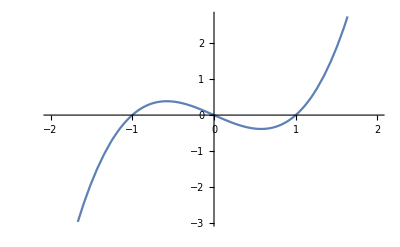

```mathematica
Plot[x^3-x,{x,-2,2}]
```

```mathematica
Abs[D[x^3-x,{x,2}]]/((√(1+D[x^3-x,x]^2))^3)
```

(6 Abs[x])/((1+(-1+3 x^2)^2)^(3/2))

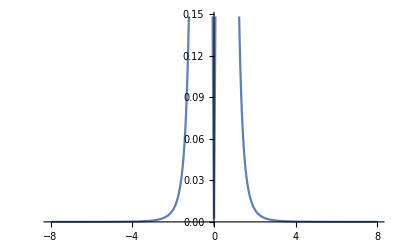

```mathematica
Plot[(6 Abs[x])/((1+(-1+3 x^2)^2)^(3/2)),{x,-8,8}]
```

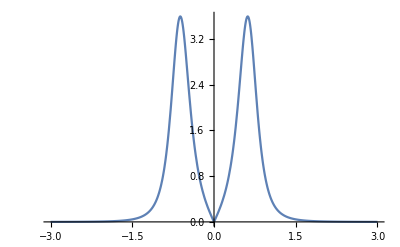

```mathematica
Plot[(6 Abs[x])/((1+(-1+3 x^2)^2)^(3/2)),{x,-3,3},PlotRange->Full]
```

```mathematica
With[{f=Function[x,x^3]},
FullSimplify[Abs[D[f[x],{x,2}]]/((√(1+D[f[x],x]^2))^3),x∈Reals]
]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

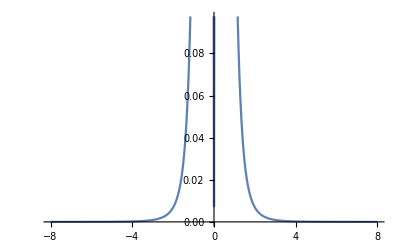

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-8,8}]
```

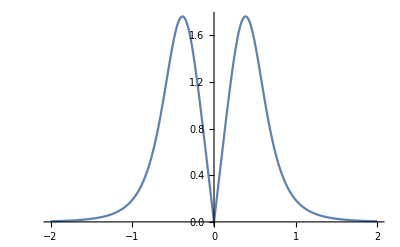

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-2,2},PlotRange->Full]
```

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[Abs[D[f[x],{x,2}]]/((√(1+D[f[x],x]^2))^3),x∈Reals]
]
```

2/((1+4 x^2)^(3/2))

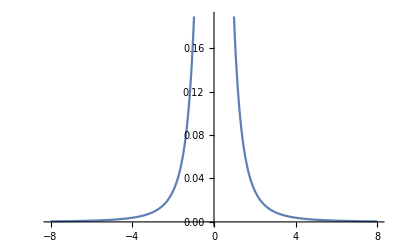

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-8,8}]
```

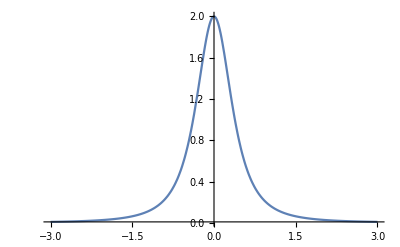

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-3,3},PlotRange->Full]
```

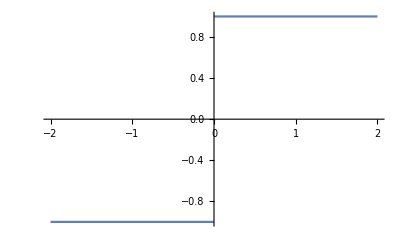

```mathematica
Plot[x/Abs[x],{x,-2,2}]
```

```mathematica
x/Abs[x]==Sign[x]
```

x/Abs[x]==Sign[x]

```mathematica
Reduce[x/Abs[x]==Sign[x]]
```

x≠0

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
Det[IdentityMatrix[2].RotationMatrix[θ]]
```

Cos[θ]^2+Sin[θ]^2

```mathematica
Simplify[Cos[θ]^2+Sin[θ]^2]
```

1

```mathematica
Det[{x'[t],y'[t]}]
```

Det::matsq: Argument {x'[t],y'[t]} at position 1 is not a non-empty square matrix.

Det[{x'[t],y'[t]}]

```mathematica
FullSimplify[Normalize@{0,2}.Normalize@{1,2x},x∈Reals]
```

(2 x)/(√(1+4 x^2))

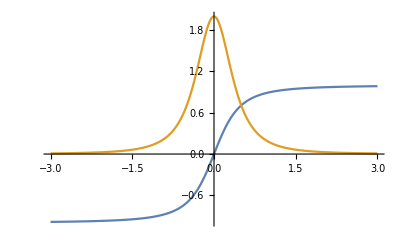

```mathematica
Plot[{(2 x)/(√(1+4 x^2)),2/((1+4 x^2)^(3/2))},{x,-3,3},PlotRange->Full]
```

```mathematica
Manipulate[
NIntegrate[(2/((1+4 x^2)^(3/2)))/a,{x,-a,a}]
,{a,.001,1000}]
```

```mathematica
Manipulate[
NIntegrate[(2/((1+4 x^2)^(3/2)))/a,{x,0,a}]
,{a,.001,1000}]
```

```mathematica
Manipulate[
NIntegrate[2/((1+4 x^2)^(3/2)),{x,0,a}]
,{a,.001,1000}]
```

```mathematica
With[{f=Function[x,x^3]},
FullSimplify[Abs[D[f[x],{x,2}]]/((√(1+D[f[x],x]^2))^3),x∈Reals]
]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-8,8}]
```

-Graphics-

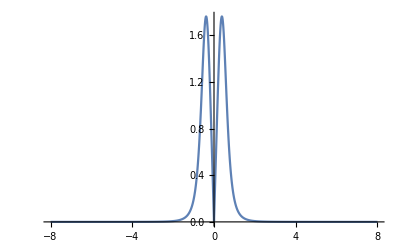

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-8,8},PlotRange->Full]
```

```mathematica
Manipulate[
NIntegrate[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,0,a}]
,{a,.001,1000}]
```

```mathematica
Manipulate[
Plot[α x^3,{x,-2,2}]
,{α,-3,3}]
```

```mathematica
Manipulate[
Plot[α x^3,{x,-2,2},PlotRange->{{-3,3},{-3,3}}]
,{α,-3,3}]
```

```mathematica
∫_0^1 √(1+D[α x^3,x]^2)ⅆx
```

ConditionalExpression[Hypergeometric2F1[-1/2,1/4,5/4,-9 α^2],Re[α^2]≥-1/9||α^2∉ℝ]

```mathematica
ConditionalExpression[Hypergeometric2F1[-1/2,1/4,5/4,-9 α^2],Re[α^2]≥-1/9||α^2∉Reals]/.α->1
```

Hypergeometric2F1[-1/2,1/4,5/4,-9]

```mathematica
N[Hypergeometric2F1[-1/2,1/4,5/4,-9]]
```

1.54787

```mathematica
Manipulate[
Plot[α x^3-x,{x,-2,2},PlotRange->{{-3,3},{-3,3}}]
,{α,-3,3}]
```

```mathematica
With[{f=Function[x,α x^3]},
FullSimplify[Abs[D[f[x],{x,2}]]/((√(1+D[f[x],x]^2))^3),x∈Reals]
]
```

(6 Abs[x α])/((1+9 x^4 α^2)^(3/2))

```mathematica
Manipulate[Plot[(6 Abs[x α])/((1+9 x^4 α^2)^(3/2)),{x,-14.608835557299809,14.608835557299809}],{α,-6.577266490803345,6.577266490803345}]
```

```mathematica
Manipulate[
Plot[(6 Abs[x α])/((1+9 x^4 α^2)^(3/2)),{x,-3,3},PlotRange->Full]
,{α,-6,6}]
```

```mathematica
Manipulate[
Plot[(6 Abs[x α])/((1+9 x^4 α^2)^(3/2)),{x,-3,3},PlotRange->{{-6,6},{-5,5}}]
,{α,-6,6}]
```

```mathematica
Manipulate[
Plot[(6 Abs[x α])/((1+9 x^4 α^2)^(3/2)),{x,-3,3},PlotRange->{{-3,3},{-5,5}}]
,{α,-6,6}]
```

```mathematica
FullSimplify[Normalize@{x,x^3},x∈Reals]
```

{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4))}

```mathematica
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√((x^3)^2+x^2)}
```

{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√(x^2+x^6)}

```mathematica
ParametricPlot3D[
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√(x^2+x^6)}
,{x,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√(x^2+x^6)},
{x,x^3,0}
},{x,-2,2}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[{
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√(x^2+x^6)},
{x,x^3,0}
},{x,-2,-2+α}]
,{α,.001,10}]
```

```mathematica
Manipulate[
ParametricPlot3D[{
{x/(√(x^2+x^6)),(x Abs[x])/(√(1+x^4)),√(x^2+x^6)},
{x,x^3,0}
},{x,-2,-2+α},PlotRange->{{-2,2},{-2,2},{-2,2}}]
,{α,.001,10}]
```

```mathematica
ParametricPlot3D[
{Cos[t],Sin[t],t}
,{t,0,2π}]
```

-Graphics3D-

```mathematica
FullSimplify[Normalize@{Cos[t],Sin[t],t},t∈Reals]
```

{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))}

```mathematica
ParametricPlot3D[
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))}
,{t,-2π,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{Cos[t],Sin[t],t}
},{t,-2π,2π}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{Cos[t],Sin[t],t}
},{t,-2π,-2π+a}]
,{a,0.01,8π}]
```

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{Cos[t],Sin[t],t}
},{t,-2π,-2π+a},PlotRange->{{-2,2},{-2,2},{-2,2}}]
,{a,0.01,8π}]
```

```mathematica
Manipulate[
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{Cos[t],Sin[t],t}
},{t,-8π,-8π+a},PlotRange->{{-2,2},{-2,2},{-2,2}}]
,{a,0.01,16π}]
```

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][u,v]
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}
,{t,0,2π},{v,0,2π}],
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{Cos[t],Sin[t],t}
},{t,-8π,-8π+a},PlotRange->{{-2,2},{-2,2},{-2,2}}]
}],{a,0.01,16π}]
```

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][t,v]
```

{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}

```mathematica
CountryData["Denmark","Population"]
```

5733551 people

```mathematica
CountryData["Israel","Population"]
```

8321570 people

```mathematica
CountryData["Netherlands","Population"]
```

17035938 people

```mathematica
CountryData["Netherlands","GDP"]
```

7.77228×10^11 $

```mathematica
CountryData["Denmark","GDP"]
```

3.069×10^11 $

```mathematica
CountryData["Israel","GDP"]
```

2.96075×10^11 $

```mathematica
CountryData["Israel","GDPPerCapita"]
```

37292.6 $

```mathematica
CountryData["Denmark","GDPPerCapita"]
```

53417.7 $

```mathematica
CountryData["Netherlands","GDPPerCapita"]
```

45294.8 $

```mathematica
Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData["Europe"]]
```

{{Albania,4146.9 $},{Andorra,36988.6 $},{Austria,44176.5 $},{Belarus,4989.25 $},{Belgium,41096.2 $},{Bosnia and Herzegovina,4708.72 $},{Bulgaria,7350.8 $},{Croatia,12090.7 $},{Cyprus,23324.2 $},{Czech Republic,18266.5 $},{Denmark,53417.7 $},{Estonia,17574.7 $},{Faroe Islands,54117.8 $},{Finland,43090.2 $},{France,36855. $},{Germany,41936.1 $},{Gibraltar,38200. $},{Greece,18104. $},{Guernsey,44600. $},{Hungary,12664.8 $},{Iceland,59976.9 $},{Ireland,61606.5 $},{Isle of Man,81672. $},{Italy,30527.3 $},{Jersey,57000. $},{Kosovo,3661.43 $},{Latvia,14118.1 $},{Liechtenstein,168146. $},{Lithuania,14879.7 $},{Luxembourg,102831. $},{Macedonia,5237.15 $},{Malta,25058.2 $},{Moldova,1843.24 $},{Monaco,163352. $},{Montenegro,6701. $},{Netherlands,45294.8 $},{Norway,70812.5 $},{Poland,12372.4 $},{Portugal,19813.3 $},{Romania,9474.13 $},{San Marino,47908.6 $},{Serbia,5348.29 $},{Slovakia,16496. $},{Slovenia,21304.6 $},{Spain,26528.5 $},{Svalbard,Missing[NotAvailable]},{Sweden,51599.9 $},{Switzerland,78812.7 $},{Ukraine,2185.73 $},{United Kingdom,39899.4 $},{Vatican City,Missing[NotAvailable]}}

```mathematica
TakeLargestBy[Map[{#,CountryData[#,"GDPPerCapita"]}&,CountryData["Europe"]],Last,10]
```

{{Liechtenstein,168146. $},{Monaco,163352. $},{Luxembourg,102831. $},{Isle of Man,81672. $},{Switzerland,78812.7 $},{Norway,70812.5 $},{Ireland,61606.5 $},{Iceland,59976.9 $},{Jersey,57000. $},{Faroe Islands,54117.8 $}}

```mathematica
TakeLargestBy[Map[{#,CountryData[#,"Population"]CountryData[#,"GDPPerCapita"]}&,CountryData["Europe"]],Last,10]
```

Quantity::compatu: Incompatible units.

TakeLargestBy[{{Albania,1.21512×10^10 $},{Andorra,2.84683×10^9 $},{Austria,3.85902×10^11 $},{Belarus,4.72399×10^10 $},{Belgium,4.69702×10^11 $},{Bosnia and Herzegovina,1.65136×10^10 $},{Bulgaria,5.20772×10^10 $},{Croatia,5.06521×10^10 $},{Cyprus,2.75121×10^10 $},{Czech Republic,1.9396×10^11 $},{Denmark,3.06273×10^11 $},{Estonia,2.30164×10^10 $},{Faroe Islands,2.66747×10^9 $},{Finland,2.37997×10^11 $},{France,2.39482×10^12 $},{Germany,3.44355×10^12 $},{Gibraltar,1.32061×10^9 $},{Greece,2.02036×10^11 $},{Guernsey,2.92598×10^9 $},{Hungary,1.23122×10^11 $},{Iceland,2.00938×10^10 $},{Ireland,2.93349×10^11 $},{Isle of Man,6.88389×10^9 $},{Italy,1.8121×10^12 $},{Jersey,5.45672×10^9 $},{Kosovo,6.80734×10^9 $},{Latvia,2.75256×10^10 $},{Liechtenstein,6.37643×10^9 $},{Lithuania,4.30067×10^10 $},{Luxembourg,5.99974×10^10 $},{Macedonia,1.09098×10^10 $},{Malta,1.07959×10^10 $},{Moldova,7.46737×10^9 $},{Monaco,6.32089×10^9 $},{Montenegro,4.21466×10^9 $},{Netherlands,7.71639×10^11 $},{Norway,3.75687×10^11 $},{Poland,4.72264×10^11 $},{Portugal,2.04662×10^11 $},{Romania,1.86444×10^11 $},{San Marino,1.60015×10^9 $},{Serbia,4.70146×10^10 $},{Slovakia,8.98646×10^10 $},{Slovenia,4.4313×10^10 $},{Spain,1.22971×10^12 $},{Svalbard,Missing[NotAvailable] (2637 people)},{Sweden,5.11391×10^11 $},{Switzerland,6.68016×10^11 $},{Ukraine,9.66593×10^10 $},{United Kingdom,2.6406×10^12 $},{Vatican City,Missing[NotAvailable] (792 people)}},Last,10]

```mathematica
TakeLargestBy[Map[{#,CountryData[#,"Population"]CountryData[#,"GDP"]}&,CountryData["Europe"]],Last,10]
```

Quantity::compatu: Incompatible units.

TakeLargestBy[{{Albania,3.47633×10^16 $},{Andorra,2.20006×10^14 $},{Austria,3.41381×10^18 $},{Belarus,4.48868×10^17 $},{Belgium,5.34842×10^18 $},{Bosnia and Herzegovina,5.93046×10^16 $},{Bulgaria,3.77168×10^17 $},{Croatia,2.12463×10^17 $},{Cyprus,2.36465×10^16 $},{Czech Republic,2.07381×10^18 $},{Denmark,1.75962×10^18 $},{Estonia,3.05641×10^16 $},{Faroe Islands,1.28817×10^14 $},{Finland,1.31731×10^18 $},{France,1.60204×10^20 $},{Germany,2.85577×10^20 $},{Gibraltar,3.82355×10^13 $},{Greece,2.15039×10^18 $},{Guernsey,1.79889×10^14 $},{Hungary,1.22313×10^18 $},{Iceland,6.71638×10^15 $},{Ireland,1.45144×10^18 $},{Isle of Man,5.72512×10^14 $},{Italy,1.10345×10^20 $},{Jersey,4.88233×10^14 $},{Kosovo,1.23635×10^16 $},{Latvia,5.37577×10^16 $},{Liechtenstein,2.38498×10^14 $},{Lithuania,1.23528×10^17 $},{Luxembourg,3.42087×10^16 $},{Macedonia,2.27056×10^16 $},{Malta,4.73877×10^15 $},{Moldova,2.65401×10^16 $},{Monaco,2.35068×10^14 $},{Montenegro,2.75115×10^15 $},{Netherlands,1.32408×10^19 $},{Norway,1.9687×10^18 $},{Poland,1.79923×10^19 $},{Portugal,2.11586×10^18 $},{Romania,3.69168×10^18 $},{San Marino,5.31296×10^13 $},{Serbia,3.36678×10^17 $},{Slovakia,4.89029×10^17 $},{Slovenia,9.29928×10^16 $},{Spain,5.73521×10^19 $},{Svalbard,Missing[NotAvailable] (2637 people)},{Sweden,5.09866×10^18 $},{Switzerland,5.66919×10^18 $},{Ukraine,4.1247×10^18 $},{United Kingdom,1.75242×10^20 $},{Vatican City,Missing[NotAvailable] (792 people)}},Last,10]

```mathematica
Grid@
TakeLargestBy[
Map[{#,CountryData[#,"Population"]CountryData[#,"GDP"]}&,CountryData["Europe"]],Last,10]
```

Quantity::compatu: Incompatible units.

Grid[TakeLargestBy[{{Albania,3.47633×10^16 $},{Andorra,2.20006×10^14 $},{Austria,3.41381×10^18 $},{Belarus,4.48868×10^17 $},{Belgium,5.34842×10^18 $},{Bosnia and Herzegovina,5.93046×10^16 $},{Bulgaria,3.77168×10^17 $},{Croatia,2.12463×10^17 $},{Cyprus,2.36465×10^16 $},{Czech Republic,2.07381×10^18 $},{Denmark,1.75962×10^18 $},{Estonia,3.05641×10^16 $},{Faroe Islands,1.28817×10^14 $},{Finland,1.31731×10^18 $},{France,1.60204×10^20 $},{Germany,2.85577×10^20 $},{Gibraltar,3.82355×10^13 $},{Greece,2.15039×10^18 $},{Guernsey,1.79889×10^14 $},{Hungary,1.22313×10^18 $},{Iceland,6.71638×10^15 $},{Ireland,1.45144×10^18 $},{Isle of Man,5.72512×10^14 $},{Italy,1.10345×10^20 $},{Jersey,4.88233×10^14 $},{Kosovo,1.23635×10^16 $},{Latvia,5.37577×10^16 $},{Liechtenstein,2.38498×10^14 $},{Lithuania,1.23528×10^17 $},{Luxembourg,3.42087×10^16 $},{Macedonia,2.27056×10^16 $},{Malta,4.73877×10^15 $},{Moldova,2.65401×10^16 $},{Monaco,2.35068×10^14 $},{Montenegro,2.75115×10^15 $},{Netherlands,1.32408×10^19 $},{Norway,1.9687×10^18 $},{Poland,1.79923×10^19 $},{Portugal,2.11586×10^18 $},{Romania,3.69168×10^18 $},{San Marino,5.31296×10^13 $},{Serbia,3.36678×10^17 $},{Slovakia,4.89029×10^17 $},{Slovenia,9.29928×10^16 $},{Spain,5.73521×10^19 $},{Svalbard,Missing[NotAvailable] (2637 people)},{Sweden,5.09866×10^18 $},{Switzerland,5.66919×10^18 $},{Ukraine,4.1247×10^18 $},{United Kingdom,1.75242×10^20 $},{Vatican City,Missing[NotAvailable] (792 people)}},Last,10]]

```mathematica
Grid@
ReverseSortBy[
Map[{#,CountryData[#,"Population"]CountryData[#,"GDP"]}&,CountryData["Europe"]],Last]
```

Germany | 2.85577×10^20 $
United Kingdom | 1.75242×10^20 $
France | 1.60204×10^20 $
Italy | 1.10345×10^20 $
Spain | 5.73521×10^19 $
Poland | 1.79923×10^19 $
Netherlands | 1.32408×10^19 $
Switzerland | 5.66919×10^18 $
Belgium | 5.34842×10^18 $
Sweden | 5.09866×10^18 $
Ukraine | 4.1247×10^18 $
Romania | 3.69168×10^18 $
Austria | 3.41381×10^18 $
Greece | 2.15039×10^18 $
Portugal | 2.11586×10^18 $
Czech Republic | 2.07381×10^18 $
Norway | 1.9687×10^18 $
Denmark | 1.75962×10^18 $
Ireland | 1.45144×10^18 $
Finland | 1.31731×10^18 $
Hungary | 1.22313×10^18 $
Slovakia | 4.89029×10^17 $
Belarus | 4.48868×10^17 $
Bulgaria | 3.77168×10^17 $
Serbia | 3.36678×10^17 $
Croatia | 2.12463×10^17 $
Lithuania | 1.23528×10^17 $
Slovenia | 9.29928×10^16 $
Bosnia and Herzegovina | 5.93046×10^16 $
Latvia | 5.37577×10^16 $
Albania | 3.47633×10^16 $
Luxembourg | 3.42087×10^16 $
Estonia | 3.05641×10^16 $
Moldova | 2.65401×10^16 $
Cyprus | 2.36465×10^16 $
Macedonia | 2.27056×10^16 $
Kosovo | 1.23635×10^16 $
Iceland | 6.71638×10^15 $
Malta | 4.73877×10^15 $
Montenegro | 2.75115×10^15 $
Isle of Man | 5.72512×10^14 $
Jersey | 4.88233×10^14 $
Liechtenstein | 2.38498×10^14 $
Monaco | 2.35068×10^14 $
Andorra | 2.20006×10^14 $
Guernsey | 1.79889×10^14 $
Faroe Islands | 1.28817×10^14 $
San Marino | 5.31296×10^13 $
Gibraltar | 3.82355×10^13 $
Svalbard | Missing[NotAvailable] (2637 people)
Vatican City | Missing[NotAvailable] (792 people)

```mathematica
Grid@
ReverseSortBy[
Map[{#,CountryData[#,"GDP"]}&,CountryData["Europe"]],Last]
```

Germany | 3.4778×10^12 $
United Kingdom | 2.6479×10^12 $
France | 2.46545×10^12 $
Italy | 1.85891×10^12 $
Spain | 1.23726×10^12 $
Netherlands | 7.77228×10^11 $
Switzerland | 6.68851×10^11 $
Sweden | 5.1446×10^11 $
Poland | 4.71364×10^11 $
Belgium | 4.67956×10^11 $
Austria | 3.908×10^11 $
Norway | 3.71076×10^11 $
Denmark | 3.069×10^11 $
Ireland | 3.04819×10^11 $
Finland | 2.38503×10^11 $
Portugal | 2.04837×10^11 $
Czech Republic | 1.95305×10^11 $
Greece | 1.92691×10^11 $
Romania | 1.87592×10^11 $
Hungary | 1.25817×10^11 $
Ukraine | 9.32705×10^10 $
Slovakia | 8.97686×10^10 $
Luxembourg | 5.86313×10^10 $
Bulgaria | 5.32379×10^10 $
Croatia | 5.0715×10^10 $
Belarus | 4.74072×10^10 $
Slovenia | 4.47086×10^10 $
Lithuania | 4.27389×10^10 $
Serbia | 3.82999×10^10 $
Latvia | 2.75727×10^10 $
Estonia | 2.33379×10^10 $
Iceland | 2.00474×10^10 $
Cyprus | 2.0047×10^10 $
Bosnia and Herzegovina | 1.69103×10^10 $
Albania | 1.18639×10^10 $
Malta | 1.0999×10^10 $
Macedonia | 1.08996×10^10 $
Isle of Man | 6.79242×10^9 $
Kosovo | 6.64989×10^9 $
Moldova | 6.55116×10^9 $
Liechtenstein | 6.28917×10^9 $
Monaco | 6.07488×10^9 $
Jersey | 5.1×10^9 $
Montenegro | 4.37413×10^9 $
Andorra | 2.85852×10^9 $
Guernsey | 2.742×10^9 $
Faroe Islands | 2.61346×10^9 $
San Marino | 1.59071×10^9 $
Gibraltar | 1.106×10^9 $
Vatican City | Missing[NotAvailable]
Svalbard | Missing[NotAvailable]

```mathematica
LaplaceTransform[(1-Exp[-2t])/t^2,t,s]
```

LaplaceTransform[(1-ⅇ^(-2 t))/t^2,t,s]

```mathematica
Abs'[x]
```

Abs'[x]

```mathematica
Abs'''''''''''[x]
```

Abs^(11)[x]

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}
,{t,0,2π},{v,0,2π}],
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))+1},
{Cos[t],Sin[t],t}
},{t,-8π,-8π+a},PlotRange->{{-2,2},{-2,2},{-2,2}}]
}],{a,0.01,16π}]
```

```mathematica
CountryData["Finland","Population"]
```

5523231 people

```mathematica
CountryData["Finland","GDP"]
```

2.38503×10^11 $

```mathematica
Sin[1/x]
```

Sin[1/x]

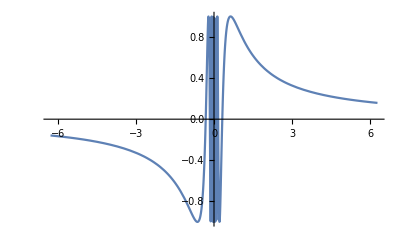

```mathematica
Plot[Sin[1/x],{x,-2 π,2 π}]
```

```mathematica
Sin[1/x]^-1
```

Csc[1/x]

Power::infy: Infinite expression 1/0. encountered.

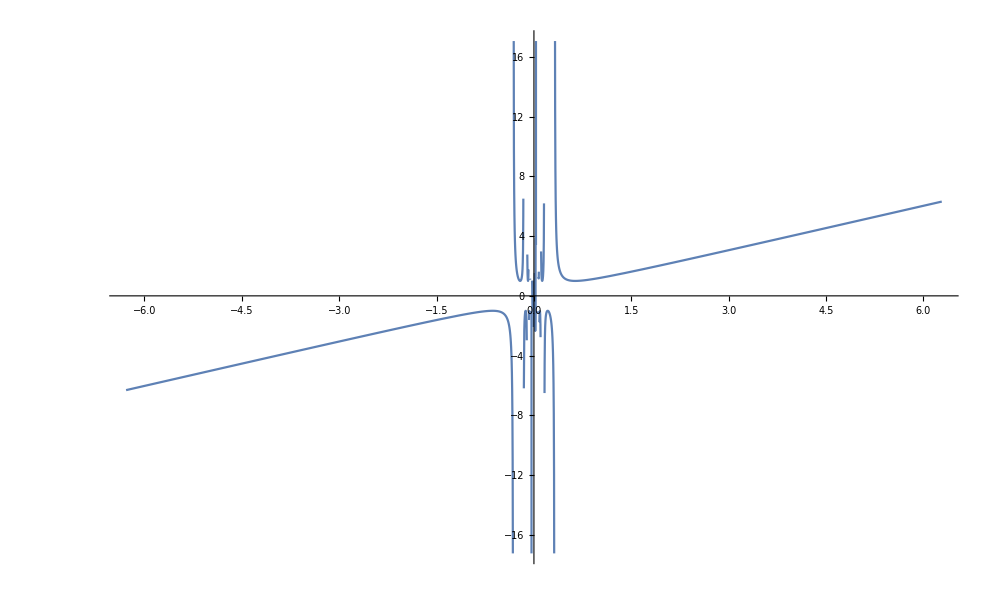

```mathematica
Plot[Csc[1/x],{x,-2 π,2 π}]
```

```mathematica
ParametricPlot3D[
{t^2 Cos[t],t^2 Sin[t],t}
,{t,-2π,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{t^2 Cos[t],t^2 Sin[t],t}
,{t,-8π,8π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{t Cos[t],t Sin[t],t}
,{t,-8π,8π}]
```

-Graphics3D-

```mathematica
FullSimplify[Normalize@{t Cos[t],t Sin[t],t},t∈Reals]
```

{(t Cos[t])/(√2 Abs[t]),(t Sin[t])/(√2 Abs[t]),t/(√2 Abs[t])}

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}
,{t,0,2π},{v,0,2π}],
ParametricPlot3D[{
{(t Cos[t])/(√2 Abs[t]),(t Sin[t])/(√2 Abs[t]),t/(√2 Abs[t])},
{t Cos[t],t Sin[t],t}
},{t,-8π,-8π+a},PlotRange->{{-2,2},{-2,2},{-2,2}}]
}],{a,0.01,16π}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot3D[
{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}
,{t,0,2π},{v,0,2π}],
ParametricPlot3D[{
{(t Cos[t])/(√2 Abs[t]),(t Sin[t])/(√2 Abs[t]),t/(√2 Abs[t])},
{t Cos[t],t Sin[t],t}
},{t,-8π,-8π+a},PlotRange->Full]
}],{a,0.01,16π}]
```

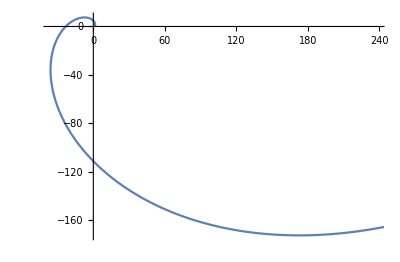

```mathematica
ParametricPlot[
{Exp[t]Cos[t],Exp[t]Sin[t]}
,{t,0,2π}]
```

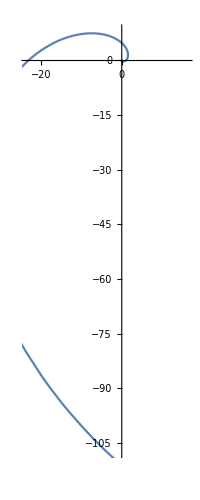

```mathematica
ParametricPlot[
{Exp[t]Cos[t],Exp[t]Sin[t]}
,{t,-2π,2π}]
```

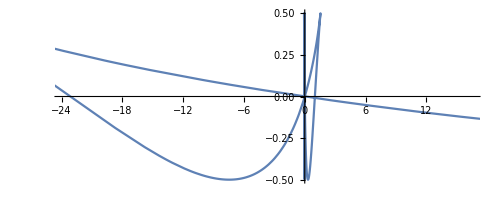

```mathematica
ParametricPlot[
{Exp[t]Cos[t],Cos[t]Sin[t]}
,{t,-2π,2π}]
```

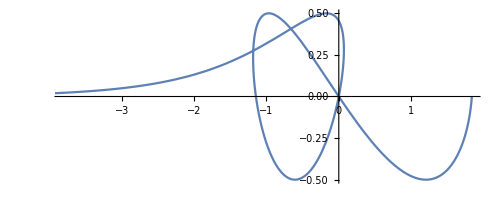

```mathematica
ParametricPlot[
{Log[t]Cos[t],Cos[t]Sin[t]}
,{t,-2π,2π}]
```

```mathematica
Sqrt[x]==x/Sqrt[x]
```

True

```mathematica
Laplacian[x^2+y^2==1,{x,y}]
```

2 False

```mathematica
Laplacian[x^2+y^2,{x,y}]
```

4

```mathematica
Laplacian[√(1-x^2-y^2),{x,y}]
```

-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))

```mathematica
Simplify[-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))]
```

(-2+x^2+y^2)/((1-x^2-y^2)^(3/2))

```mathematica
Plot3D[(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),{x,y}∈Disk[]]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
Plot3D[(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),{x,y}∈Disk[],PlotRange->Full]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
FullSimplify[Integrate[Normalize@D[{Cos[t],Sin[t],t},t],t],t∈Reals]
```

{Cos[t]/(√2),Sin[t]/(√2),t/(√2)}

```mathematica
ParametricPlot3D[{
{Cos[t]/(√2),Sin[t]/(√2),t/(√2)},
{Cos[t],Sin[t],t}
},{t,0,2π}]
```

-Graphics3D-